# CKT Classic 1

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pcs/Desktop/Breaking time reversal symmetry/Klein group

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[F,Fun,Funinv];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Funinv[α_,k_,s_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},-1].s
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

Clear[mapeoinv];
mapeoinv[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funinv[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

```mathematica
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
```

## Poincare maps

```mathematica
Clear[rot];
rot[θ_]:={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
Clear[Tx,Ty,Tz];
Tx=DiagonalMatrix[{1,-1,-1}];
Ty=DiagonalMatrix[{-1,1,-1}];
Tz=DiagonalMatrix[{-1,-1,1}];
Clear[T1,T2,T3];
T1[α_]:={{-Cos[α],-Sin[α],0},{-Sin[α],Cos[α],0},{0,0,1}};
T2[α_]:={{Cos[α],Sin[α],0},{Sin[α],-Cos[α],0},{0,0,1}};
T3=Tz;
Clear[Rz];
Rz[α_]:={{Cos[α],-Sin[α],0},{Sin[α],Cos[α],0},{0,0,1}};
Clear[com];
com[a_,b_]:=a.b-b.a;
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];
```

```mathematica
Clear[Rx,Rz,Rxx,Rzz];
Rz[α_,τ_]:={{Cos[α*τ],-Sin[α*τ],0},{Sin[α*τ],Cos[α*τ],0},{0,0,1}};
Rxx[k_,s_]:={{1,0,0},{0,Cos[k*s[[1]]],-Sin[k*s[[1]]]},{0,Sin[k*s[[1]]],Cos[k*s[[1]]]}};
Rx[k_]:={{1,0,0},{0,Cos[k],-Sin[k]},{0,Sin[k],Cos[k]}};
Rzz[α_,τ_,s_]:={{Cos[α*τ*s[[3]]],-Sin[α*τ*s[[3]]],0},{Sin[α*τ*s[[3]]],Cos[α*τ*s[[3]]],0},{0,0,1}};
Clear[map1,map2];
map1[α_,τ_,k_,s_,n_]:=NestList[Rz[α,τ].Rxx[k,#].#&,s,n];
map2[α_,τ_,k_,s_,n_]:=NestList[Rx[k].Rzz[α,τ,#].#&,s,n];
```

```mathematica
τ=1;
α=0.84;
k=8.;
```

```mathematica
ini=RandomPoint[Disk[{0,0},1.999],2];
```

```mathematica
ini=Table[{i,0},{i,-1.999,1.999,0.001}];
ini=Map[rot[α/2].#&,ini];
```

```mathematica
ini=Table[{0,i},{i,-1.999,1.999,0.001}];
ini=Map[rot[α/2].#&,ini];
```

```mathematica
ini=Table[{i,0},{i,-1.999,1.999,0.001}];
```

```mathematica
kicks=1000;
poincare=ParallelTable[mapeo[i,α,k,kicks],{i,ini},DistributedContexts->Full];
```

```mathematica
Clear[T1,T2,T3];
T1[α_]:={{-Cos[α],-Sin[α]},{-Sin[α],Cos[α]}};
T2[α_]:={{Cos[α],Sin[α]},{Sin[α],-Cos[α]}};
```

```mathematica
poincare1=Map[T1[α].#&,poincare];
poincare2=Map[T2[α].#&,poincare];
```

```mathematica
ListPlot[poincare,PlotRange->All,AspectRatio->1,ImageSize->800,PlotLegends->{Style["original",18],Style["T1",18],Style["T2",18]}]
```

## Powers of Poincaré

```mathematica
Clear[mapeop];
mapeop[Qini_,α_,k_,n_,p_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funp[α,k,#,p]&,s,n];
Map[change[#]&,list]
];
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};

Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},p].s
];
(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a},
a=F[α,k,point];
MatrixPower[a.mat,p].s
];*)

(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a,b},
a=F[α,k,point];
b=F[α,k,a.point];
MatrixPower[b.a.mat,p].s
];*)

(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a,b,c},
a=F[α,k,point];
b=F[α,k,a.point];
c=F[α,k,b.(a.point)];
MatrixPower[c.b.a.mat,p].s
];*)

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];
```

```mathematica
Clear[α,k];
α=0.84;
τ=1;
```

```mathematica
line=Table[{Rationalize[i],0},{i,-1999/1000,1999/1000,1/25000}];
sym=ParallelTable[rot[α/2].i,{i,line}];
symb=Table[rot[Pi/2].i,{i,sym}];
k=20.;
(*region=Join[sym,symb];*)
region=sym;
```

```mathematica
kicks=1;
puntos=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,region},DistributedContexts->Full];
newpoincarea=puntos[[All,-1]];
powerone=Graphics[{PointSize[0.0020],Black,Opacity[0.3],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->600,PlotLabel->Style["kicks = "<>ToString[kicks],20,Black]]
```

```mathematica
Clear[T1,T2,T3];
T1[α_]:={{-Cos[α],-Sin[α]},{-Sin[α],Cos[α]}};
T2[α_]:={{Cos[α],Sin[α]},{Sin[α],-Cos[α]}};
T3[α_]:={{-1,0},{0,-1}};
```

```mathematica
newpoincarea=puntos[[All,-1]];
```

```mathematica
newpoincarea=Map[T3[α].#&,newpoincarea];
```

```mathematica
poweronet1=Graphics[{PointSize[0.0020],Black,Opacity[0.3],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->600,PlotLabel->Style["kicks = "<>ToString[kicks],20,Black]];
```

```mathematica
poweronet2=Graphics[{PointSize[0.0020],Black,Opacity[0.3],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->600,PlotLabel->Style["kicks = "<>ToString[kicks],20,Black]];
```

```mathematica
poweronet3=Graphics[{PointSize[0.0020],Black,Opacity[0.3],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->600,PlotLabel->Style["kicks = "<>ToString[kicks],20,Black]];
```

```mathematica
Show[{poweronet1,poweronet2,poweronet3}]
```

```mathematica
Show[{poweronet1,poweronet2,poweronet3}]
```

```mathematica
Show[{poweronet1,poweronet2,poweronet3}]
```

```mathematica
Show[{poweronet1,poweronet2,poweronet3}]
```

```mathematica
Show[{d2plotM,Show[{powerone,poweronet1}]}]
```

```mathematica
Show[{d2plotM,Show[{powerone,poweronet1}]}]
```

```mathematica
Show[{d2plotM,Show[{powerone,poweronet1}]}]
```

```mathematica
Show[{powerone,poweronet1}]
```

```mathematica
Show[{powerone,poweronet2}]
```

```mathematica
kicks=2;
p=1;
k=20.;
line=Table[{Rationalize[i],0},{i,-1.999,1.999,1/10000}];
sym=ParallelTable[rot[α/2+0.0001].i,{i,line}];
region=sym;
```

```mathematica
region=newpoincarea;
```

```mathematica
Do[
plots={};
Do[
puntos=ParallelTable[Quiet[mapeop[i,α,k,kicks,p]],{i,region},DistributedContexts->Full];
newpoincarea=Flatten[puntos,1];
powera=Graphics[{PointSize[0.0020],Brown,Opacity[0.1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000,PlotLabel->Style["kicks = "<>ToString[kicks]<>", p 1000",20,Black]];
AppendTo[plots,powera];
,{p,{1,10,100,1000}}];
Export["poincarepower_one_c_alfa_0.84_k_5_kick_"<>ToString[kicks]<>".png",Show[{powerone,plots}],ImageResolution->300]
,{kicks,{1,2,3,4,5}}]
```

# Symmetry lines iterations

```mathematica
Clear[T1,T2,T3];
T1[α_]:={{-Cos[α],-Sin[α]},{-Sin[α],Cos[α]}};
T2[α_]:={{Cos[α],Sin[α]},{Sin[α],-Cos[α]}};
T3[α_]:={{-1,0},{0,-1}};
```

```mathematica
Clear[α,k];
α=0.84;
τ=1;
k=20.;
```

```mathematica
line=Table[{Rationalize[i],0},{i,-1999/1000,1999/1000,1/20000}];
sym=ParallelTable[rot[α/2].i,{i,line}];
symb=Table[rot[Pi/2].i,{i,sym}];
region=sym;
```

```mathematica
symsplot=Plot[{Tan[α/2]x,Tan[α/2+Pi/2]x},{x,sym[[-1]][[1]],sym[[1]][[1]]},PlotStyle->{Directive[Black,Dashed],Directive[Gray,Dashed,Opacity[0.5]]}];
```

```mathematica
kicks=1;
```

```mathematica
Do[

puntos=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,region},DistributedContexts->Full];
newpoincarea=puntos[[All,-1]];
powerone=Graphics[{PointSize[0.0010],Black,Opacity[0.30],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000,PlotLabel->Style["kicks = "<>ToString[kicks],20,Black]];
newpoincarea=puntos[[All,-1]];
transform1=Map[T1[α].#&,newpoincarea];
transform2=Map[T2[α].#&,newpoincarea];
transform3=Map[T3[α].#&,newpoincarea];
poweronet1=Graphics[{PointSize[0.0010],Black,Opacity[0.5],Point[transform1]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000,PlotLabel->Style["kicks = "<>ToString[kicks],20,Black]];
poweronet2=Graphics[{PointSize[0.0010],Blue,Opacity[0.5],Point[transform2]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000,PlotLabel->Style["kicks = "<>ToString[kicks],20,Black]];
poweronet3=Graphics[{PointSize[0.0010],Red,Opacity[0.5],Point[transform3]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000,PlotLabel->Style["kicks = "<>ToString[kicks],20,Black]];
plot=Show[{poweronet1,poweronet2,poweronet3,symsplot},ImageSize->1000];
Export["plot_fundamental2_kick_"<>ToString[kicks]<>"_.png",plot];

,{kicks,5}]
```

```mathematica
kicks=1;
puntos=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,region},DistributedContexts->Full];
newpoincarea=puntos[[All,-1]];
powerone=Graphics[{PointSize[0.0010],Black,Opacity[0.30],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000,PlotLabel->Style["kicks = "<>ToString[kicks],20,Black]];
newpoincarea=puntos[[All,-1]];
transform1=Map[T1[α].#&,newpoincarea];
transform2=Map[T2[α].#&,newpoincarea];
transform3=Map[T3[α].#&,newpoincarea];
poweronet1=Graphics[{PointSize[0.0010],Black,Opacity[0.5],Point[transform1]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000,PlotLabel->Style["kicks = "<>ToString[kicks],20,Black]];
poweronet2=Graphics[{PointSize[0.0010],Blue,Opacity[0.5],Point[transform2]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000,PlotLabel->Style["kicks = "<>ToString[kicks],20,Black]];
poweronet3=Graphics[{PointSize[0.0010],Red,Opacity[0.5],Point[transform3]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000,PlotLabel->Style["kicks = "<>ToString[kicks],20,Black]];
```

```mathematica
plot1=Show[{poweronet1,poweronet2,poweronet3,symsplot},ImageSize->1000]
```

```mathematica
plot2=Show[{poweronet1,poweronet2,poweronet3,symsplot},ImageSize->1000]
```

```mathematica
Export["plot_fundamental1and2_kick_"<>ToString[kicks]<>"_.png",Show[{plot1,plot2},ImageSize->1000]]
```

plot_fundamental1and2_kick_1_.png

```mathematica
Show[{plot1,plot2},ImageSize->700]
```

-Graphics-

# General map

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pcs/Desktop/Breaking time reversal symmetry/Klein group

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[F,Fun,Funinv];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Funinv[α_,k_,s_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},-1].s
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

Clear[mapeoinv];
mapeoinv[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funinv[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

```mathematica
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
```

## Poincare maps

```mathematica
Clear[rot];
rot[θ_]:={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
Clear[Tx,Ty,Tz];
Tx=DiagonalMatrix[{1,-1,-1}];
Ty=DiagonalMatrix[{-1,1,-1}];
Tz=DiagonalMatrix[{-1,-1,1}];
Clear[T1,T2,T3];
T1[α_]:={{-Cos[α],-Sin[α],0},{-Sin[α],Cos[α],0},{0,0,1}};
T2[α_]:={{Cos[α],Sin[α],0},{Sin[α],-Cos[α],0},{0,0,1}};
T3=Tz;
Clear[Rz];
Rz[α_]:={{Cos[α],-Sin[α],0},{Sin[α],Cos[α],0},{0,0,1}};
Clear[com];
com[a_,b_]:=a.b-b.a;
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];
```

```mathematica
Clear[Rxx,Raxis];
Raxis[theta_,n_]:=Module[{u=Normalize[n],nx,ny,nz,c=Cos[theta],s=Sin[theta]},
{nx,ny,nz}=u;
{{c+nx^2 (1-c),nx ny (1-c)-nz s,nx nz (1-c)+ny s},{ny nx (1-c)+nz s,c+ny^2 (1-c),ny nz (1-c)-nx s},{nz nx (1-c)-ny s,nz ny (1-c)+nx s,c+nz^2 (1-c)}}
];
Rxx[k_,s_]:={{1,0,0},{0,Cos[k*s[[1]]],-Sin[k*s[[1]]]},{0,Sin[k*s[[1]]],Cos[k*s[[1]]]}};
Clear[map];
map[theta_,n_,k_,s_,kicks_]:=NestList[Raxis[theta,n].Rxx[k,#].#&,s,kicks];
```

```mathematica
Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];
Clear[T1,T2];
T1[α_]:={{-Cos[α],-Sin[α]},{-Sin[α],Cos[α]}};
T2[α_]:={{Cos[α],Sin[α]},{Sin[α],-Cos[α]}};
```

```mathematica
α=0.84;
k=10.;
```

```mathematica
kicks=1500;
```

```mathematica
ini=RandomPoint[Sphere[],100];
```

```mathematica
n={0,1/3,1};
```

```mathematica
poincare=ParallelTable[map[α,n,k,i,kicks],{i,ini},DistributedContexts->Full];
qppoints=Map[change[#]&,Flatten[poincare,1]];
```

```mathematica
poincare1=Map[T1[α].#&,qppoints];
poincare2=Map[T2[α].#&,qppoints];
```

```mathematica
classic=ListPlot[qppoints,PlotRange->All,PlotStyle->Directive[Black,Opacity[1],PointSize[0.0015]],AspectRatio->1,ImageSize->800,PlotTheme->"Detailed"]
```

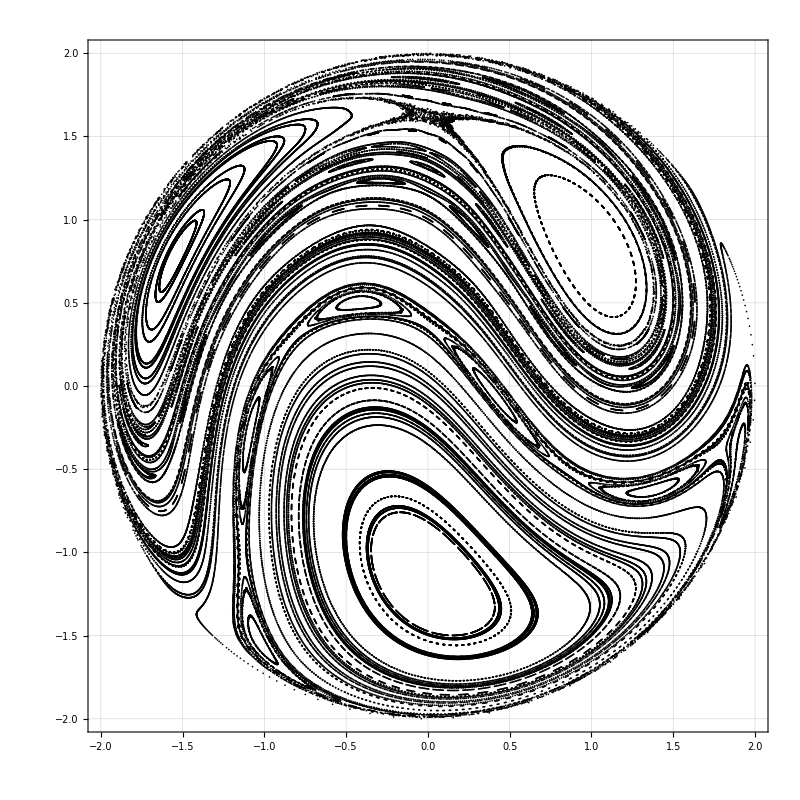

```mathematica
classic=ListPlot[qppoints,PlotRange->All,PlotStyle->Directive[Black,Opacity[1],PointSize[0.0015]],AspectRatio->1,ImageSize->800,PlotTheme->"Detailed"]
```

```mathematica
ListPlot[{poincare1,poincare2,qppoints},PlotRange->All,PlotStyle->{Directive[Blue,Opacity[0.15]],Directive[Red,Opacity[0.15]],Directive[Black,Opacity[1]]},AspectRatio->1,ImageSize->800,PlotTheme->"Detailed"]
```

## Poincare maps, breaking time reversal

```mathematica
Clear[rot];
rot[θ_]:={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
Clear[Tx,Ty,Tz];
Tx=DiagonalMatrix[{1,-1,-1}];
Ty=DiagonalMatrix[{-1,1,-1}];
Tz=DiagonalMatrix[{-1,-1,1}];
Clear[T1,T2,T3];
T1[α_]:={{-Cos[α],-Sin[α],0},{-Sin[α],Cos[α],0},{0,0,1}};
T2[α_]:={{Cos[α],Sin[α],0},{Sin[α],-Cos[α],0},{0,0,1}};
T3=Tz;
Clear[Rz,Rx];
Rx[k_]:={{1,0,0},{0,Cos[k],-Sin[k]},{0,Sin[k],Cos[k]}};
Rz[α_]:={{Cos[α],-Sin[α],0},{Sin[α],Cos[α],0},{0,0,1}};
Clear[com];
com[a_,b_]:=a.b-b.a;
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];
```

```mathematica
(*Ry[alpha_,tau_]:={{Cos[alpha*tau],0,Sin[alpha*tau]},{0,1,0},{-Sin[alpha*tau],0,Cos[alpha*tau]}}*)
```

```mathematica
Clear[Rxx,Raxis];
Raxis[theta_,n_]:=Module[{u=Normalize[n],nx,ny,nz,c=Cos[theta],s=Sin[theta]},
{nx,ny,nz}=u;
{{c+nx^2 (1-c),nx ny (1-c)-nz s,nx nz (1-c)+ny s},{ny nx (1-c)+nz s,c+ny^2 (1-c),ny nz (1-c)-nx s},{nz nx (1-c)-ny s,nz ny (1-c)+nx s,c+nz^2 (1-c)}}
];
Rxx[k_,s_]:={{1,0,0},{0,Cos[k*s[[1]]],-Sin[k*s[[1]]]},{0,Sin[k*s[[1]]],Cos[k*s[[1]]]}};
Clear[map];
map[n_,α_,k_,γ_,s_,kicks_]:=NestList[Raxis[γ,{0,1,0}].Raxis[α,n].Rxx[k,#].#&,s,kicks];
```

```mathematica
α=0.84;
k=4.;
n={1,1,1};
γ=1.;
```

```mathematica
kicks=2000;
```

```mathematica
ini=RandomPoint[Sphere[],100];
```

```mathematica
poincare=ParallelTable[map[n,α,k,γ,i,kicks],{i,ini},DistributedContexts->Full];
qppoints=Map[change[#]&,Flatten[poincare,1]];
```

```mathematica
classic=ListPlot[qppoints,PlotRange->All,PlotStyle->Directive[Black,Opacity[1],PointSize[0.0015]],AspectRatio->1,ImageSize->800,PlotTheme->"Detailed"]
```

-Graphics-

# QKT Quantum

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pcs/Desktop/Breaking time reversal symmetry/Klein group

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=SparseArray[(1/2)(SM[J]+Sm[J])];
Sy[J_]:=SparseArray[(1/(2I))(SM[J]-Sm[J])];
Qp[J_]:=DiagonalMatrix[Table[Sqrt[i/2],{i,IntegerPart[2J]}],-1];
QQ[J_]:=Qp[J]+Transpose[Qp[J]];
PP[J_]:=-I(Qp[J]-Transpose[Qp[J]]);
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
Clear[haar];
haar[dim_Integer]:=Module[{l=2*dim+1,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

## Method

```mathematica
radius=1.99;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

20107

```mathematica
nr=150;
nphi=100;
points=Flatten[Table[{2 Sqrt[u] Cos[phi],2 Sqrt[u] Sin[phi]},{u,0,1,1/nr},{phi,0,2 Pi,2 Pi/nphi}],1];
```

```mathematica
points//Dimensions
```

{15251,2}

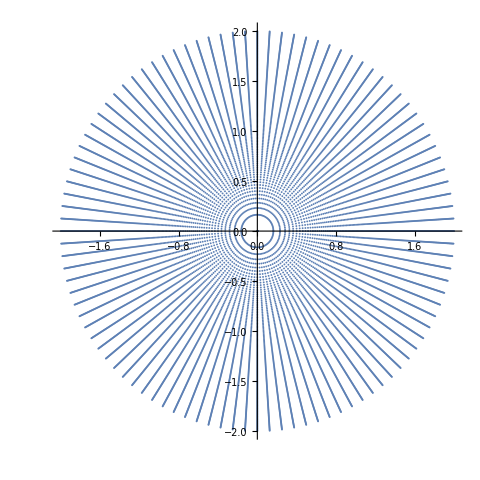

```mathematica
ListPlot[points,AspectRatio->1]
```

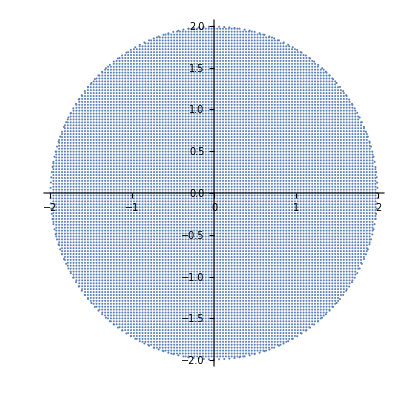

```mathematica
ListPlot[region,AspectRatio->1]
```

## Phase space

```mathematica
Clear[a2iM];
a2iM[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J,2}],18]]
];
Clear[a2im];
a2im[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J+1,J,2}],18]]
];
(*cohesM=ParallelTable[Quiet[a2iM[J,i[[1 ]],i[[2]]]],{i,region}];
cohesm=ParallelTable[Quiet[a2im[J,i[[1]],i[[2]]]],{i,region}];
Clear[husimiM,husimim];
husimiM[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohesM[[i]]].ψ]^2},{i,Length[region]}];
husimim[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohesm[[i]]].ψ]^2},{i,Length[region]}];*)
Clear[Rz,Rx,Ry];
Rx[J_,θ_]:=MatrixExp[-I(N[θ])Sx[J]];
Ry[J_,θ_]:=MatrixExp[-I(N[θ])Sy[J]];
Rz[J_,θ_]:=MatrixExp[-I(N[θ])Sz[J]];
```

```mathematica
Clear[J];
J=300;
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1 ]],i[[2]]]],{i,region},DistributedContexts->Full,Method->"CoarsestGrained"];
```

```mathematica
Clear[Floq];
Floq[J_,α_,k_,n_]:=Module[{u=Normalize[n],x=Sx[J],y=Sy[J],z=Sz[J]},
N[MatrixExp[(-I*k/(2J))(x.x)]].N[MatrixExp[(-I*α)(u.{x,y,z})]]
];
```

```mathematica
α=0.84;
k=10.0;
n={0,1/3,1};
```

```mathematica
mat=Floq[J,α,k,n];
(*mat=Rx[J,Pi/2].Ry[J,Pi/2].(Rx[J,k2/2].Floq[J,α2,k2,τ2].ConjugateTranspose[Rx[J,k2/2]]).ConjugateTranspose[Ry[J,Pi/2]].ConjugateTranspose[Rx[J,Pi/2]];*)
{eigenval,eigenvec}=Eigensystem[mat];
eigenvec=Orthogonalize[eigenvec];
(*South pole*)
(*mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;*)
(*matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];*)
(*zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
eigenval=Riffle[eigenvalM,eigenvalm];
eigenvec=Riffle[neweigenvecM,neweigenvecm];*)
```

```mathematica
q=2;
d2M=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^(2q)],{i,cohes},DistributedContexts->Full,Method->"CoarsestGrained"];
```

```mathematica
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[2J+1]}];
```

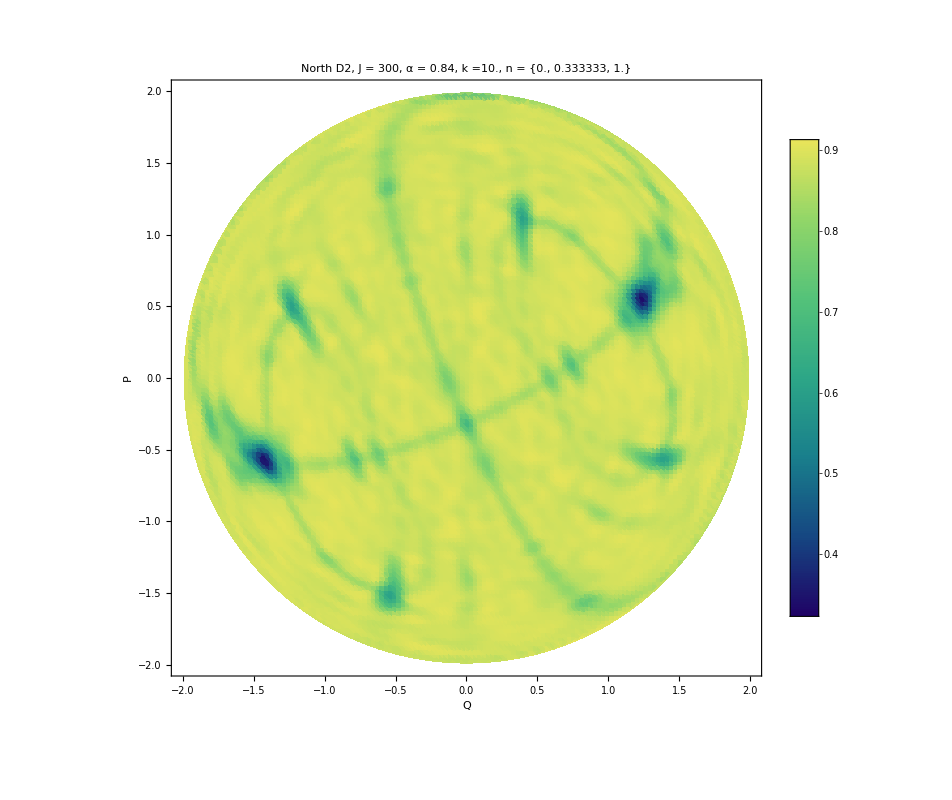

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

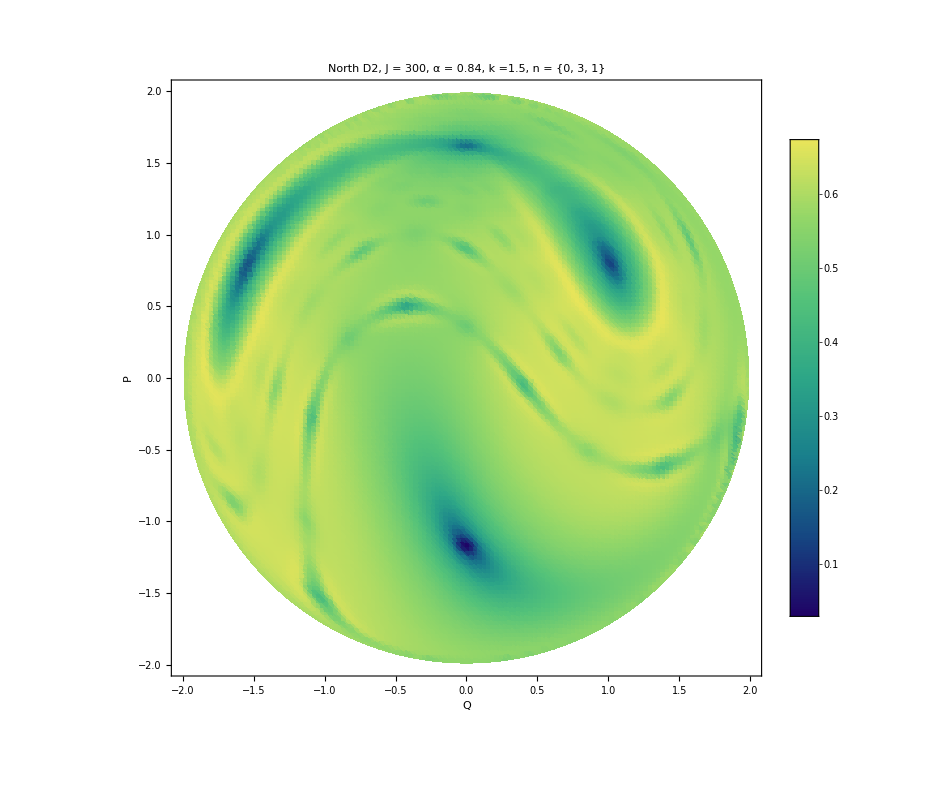

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

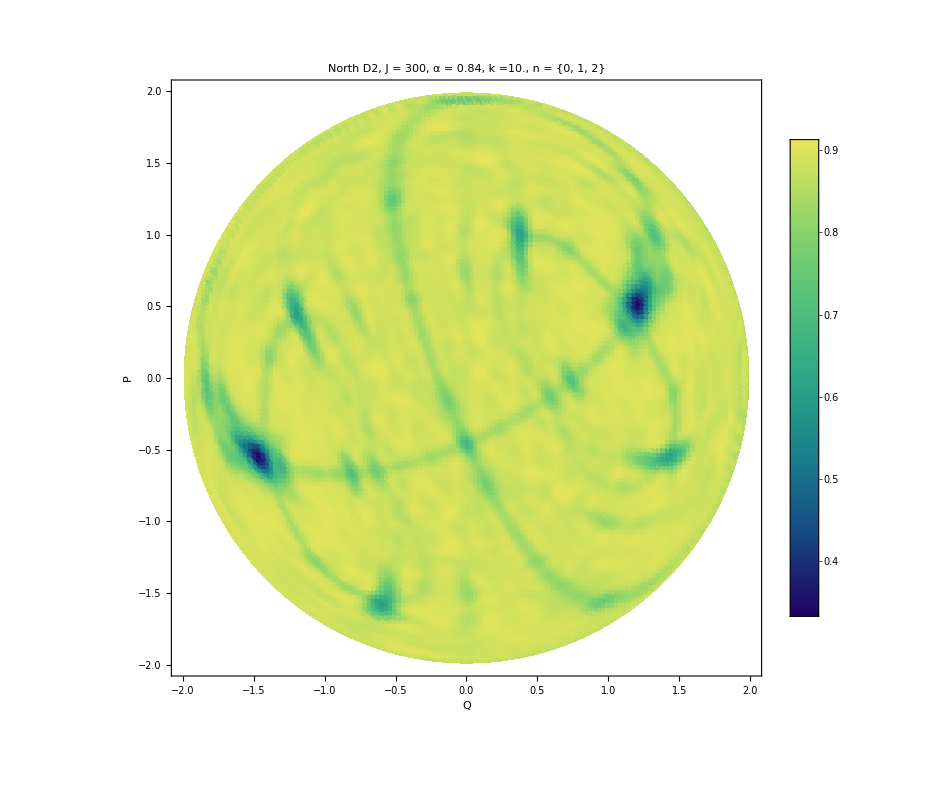

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

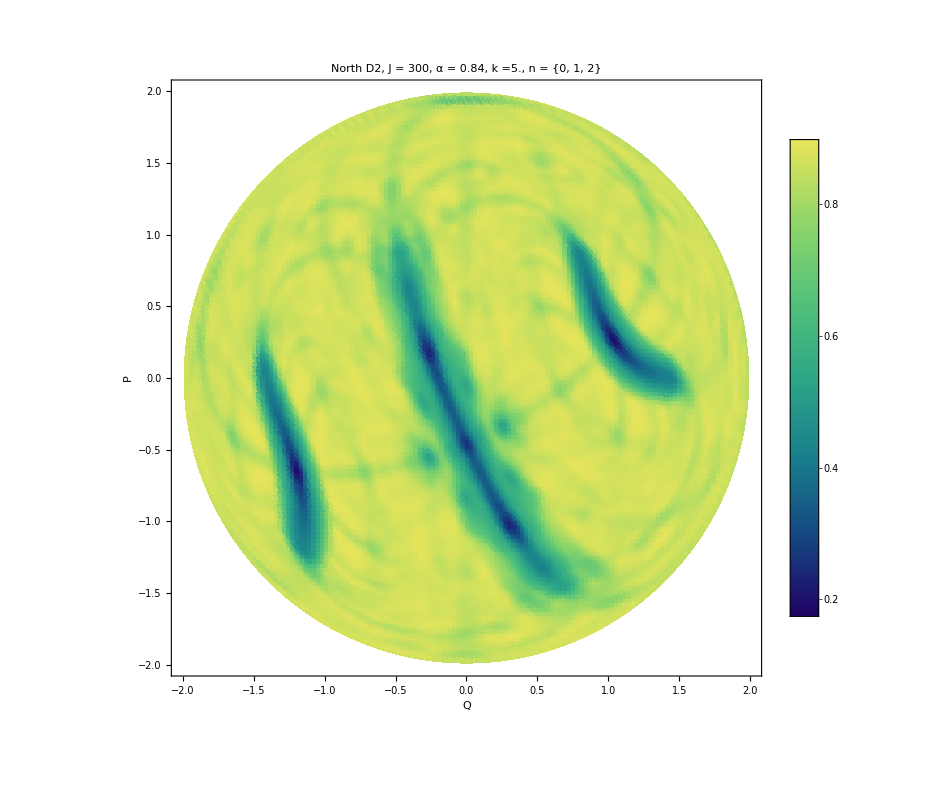

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

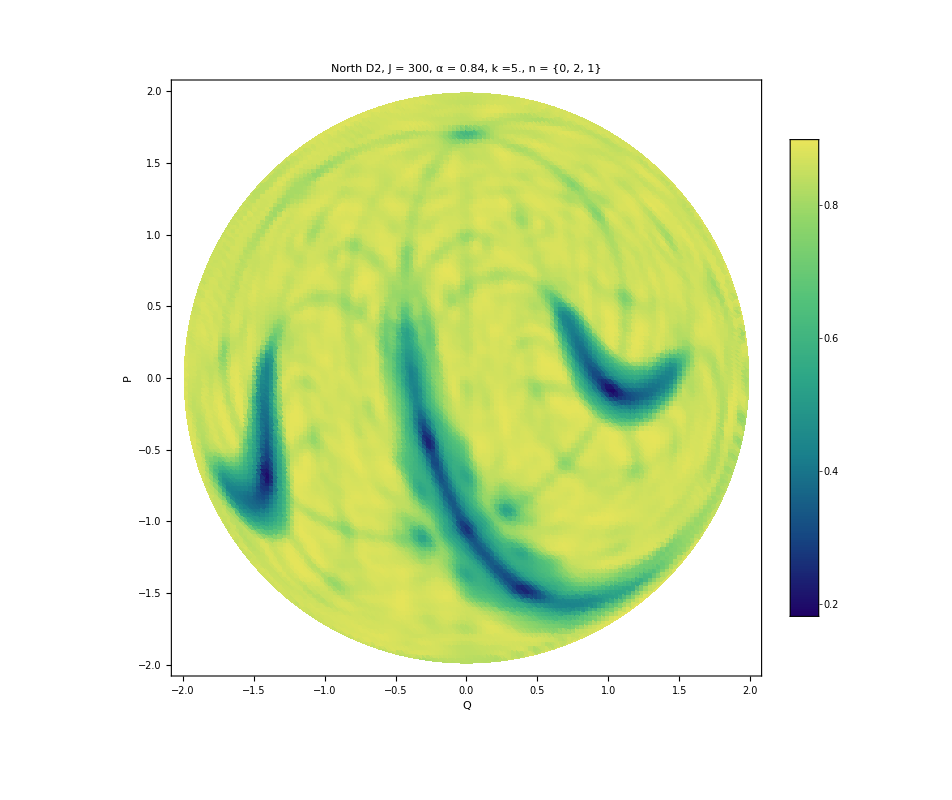

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

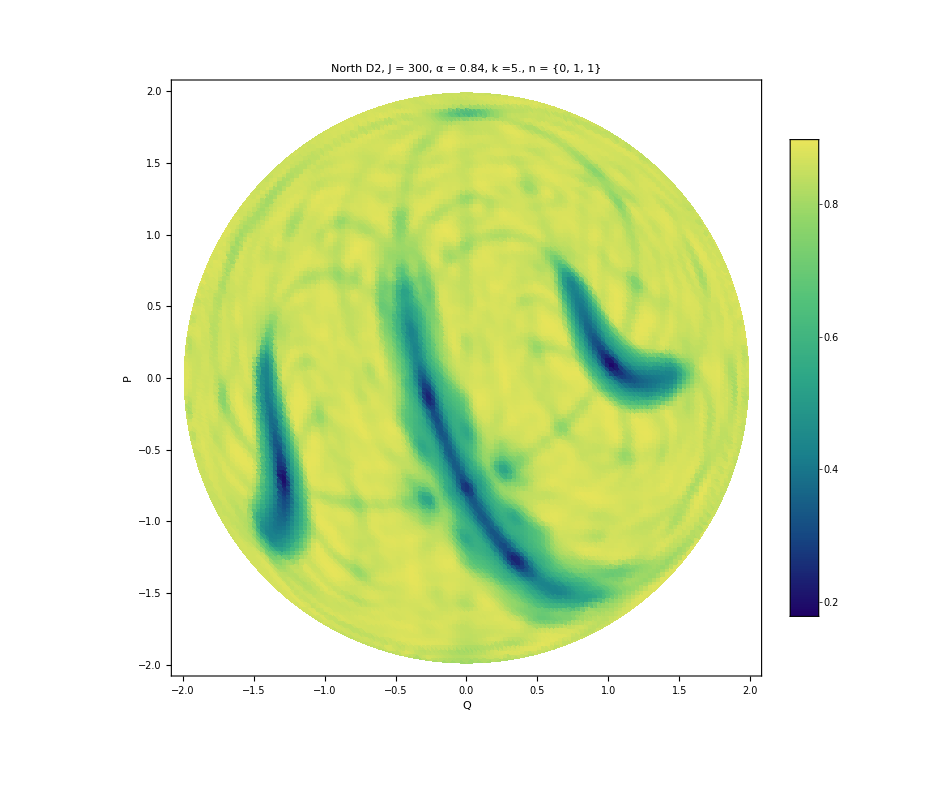

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

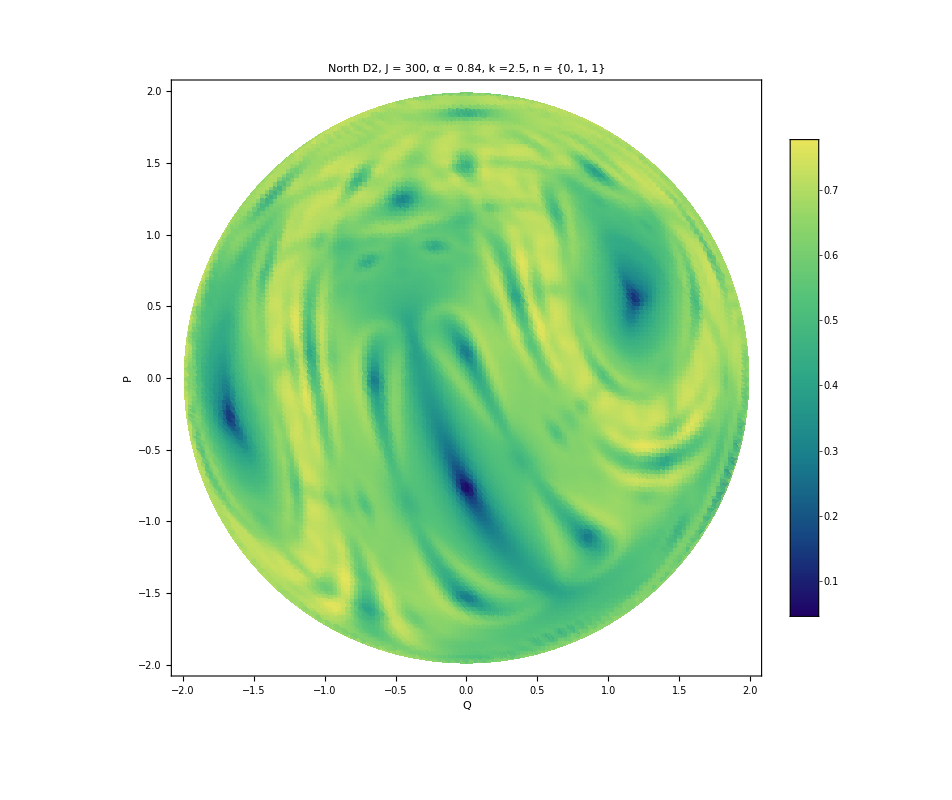

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[n],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
Show[{d2plotM,classic}]
(*Export["d2_k_5_with_lines.png",Show[{d2plotM,lines}],ImageResolution->300]*)
```

-Graphics-

## husimis and ldos

```mathematica
Clear[rotation,t1,t2];
rotation=MatrixExp[(-I)(α2)(Sz[J])];
t1[state_]:=Conjugate[rotation.state];
t2[state_]:=rotation.Conjugate[state];
```

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^2},{i,Length[region]},DistributedContexts->Full];
```

```mathematica
inicohe1=t1[a2[J,75/100,1]];
inicohe2=t2[a2[J,75/100,1]];
(*inicohe=t1[a2[J,1/2,1]];*)
ipr=ParallelTable[Abs[Conjugate[i].inicohe1]^2,{i,eigenvec}];
sorted=SortBy[Transpose[{ipr,eigenval,eigenvec}],First];
sortedeigenvec=sorted[[All,3]];
```

```mathematica
ListPlot[{Transpose[{Arg[sorted[[All,2]]],Abs[Conjugate[sortedeigenvec].inicohe1]^2}],Transpose[{Arg[sorted[[All,2]]],Abs[Conjugate[sortedeigenvec].inicohe2]^2}]},PlotRange->All,Filling->Bottom]
```

-Graphics-

```mathematica
ListPlot[sorted[[All,1]],Filling->Bottom,PlotRange->All]
ListPlot[Transpose[{Arg[sorted[[All,2]]],Abs[Conjugate[sortedeigenvec].inicohe]^2}],PlotRange->All,Filling->Bottom]
```

-Graphics-

-Graphics-

```mathematica
husistate1=husimi[sortedeigenvec[[-1]]];
husistate2=husimi[t1[sortedeigenvec[[-1]]]];
husistate3=husimi[t2[sortedeigenvec[[-1]]]];
husistate4=husimi[Rz[J,Pi].sortedeigenvec[[-1]]];
```

```mathematica
ListDensityPlot[husistate1,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->1, PerformanceGoal->"Quality",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α2]]<>", k ="<>ToString[k2]<>", τ = "<>ToString[τ2],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

## D2 Statistics

```mathematica
kicks=1;
k=20.;
line=Table[{Rationalize[i],0},{i,0,1999/1000,1/1000}];
sym=ParallelTable[rot[α/2].i,{i,line}];
region=sym;
```

```mathematica
region//Length
```

2000

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1 ]],i[[2]]]],{i,line},DistributedContexts->Full];
```

```mathematica
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
```

```mathematica
Clear[Rz,Rx,Ry];
Rx[J_,θ_]:=MatrixExp[-I(N[θ])Sx[J]];
Ry[J_,θ_]:=MatrixExp[-I(N[θ])Sy[J]];
Rz[J_,θ_]:=MatrixExp[-I(N[θ])Sz[J]];
```

```mathematica
τ2=1;
α2=0.84;
k2=20.;
```

```mathematica
mat=Floq[J,α2,k2,τ2];
(*mat=Rx[J,Pi/2].Ry[J,Pi/2].(Rx[J,k2/2].Floq[J,α2,k2,τ2].ConjugateTranspose[Rx[J,k2/2]]).ConjugateTranspose[Ry[J,Pi/2]].ConjugateTranspose[Rx[J,Pi/2]];*)
{eigenval,eigenvec}=Eigensystem[mat];
eigenvec=Orthogonalize[eigenvec];
```

```mathematica
q=2;
d2M=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^(2q)],{i,cohes},DistributedContexts->Full,Method->"CoarsestGrained"];
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[2J+1]}];
```

```mathematica
ListPlot[Transpose[{line[[All,1]],newd2M[[All,3]]}],PlotRange->All,ImageSize->800]
```

-Graphics-

```mathematica
ListPlot[newd2M[[All,3]],PlotRange->All,ImageSize->800]
```

-Graphics-

```mathematica
ListPlot[newd2M[[All,3]],PlotRange->{{1350,1450},All},ImageSize->800]
```

-Graphics-

```mathematica
plots=Table[ListPlot[Transpose[{Arg[eigenval],Quiet[Abs[Conjugate[eigenvec].cohes[[i]]]^2]}],PlotRange->{All,{0,0.015}},Filling->Bottom,ImageSize->800,PlotLabel->Style["i = "<>ToString[i],25,Black]],{i,1350,1450}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

# Breaking time reversal symmetry 1

## Phase space

```mathematica
Clear[Rz,Rx,Ry,MeanLevelSpacingRatio];
Rx[J_,θ_]:=MatrixExp[-I(N[θ])Sx[J]];
Ry[J_,θ_]:=MatrixExp[-I(N[θ])Sy[J]];
Rz[J_,θ_]:=MatrixExp[-I(N[θ])Sz[J]];
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[Sort[eigenvalues]]]]]
```

```mathematica
Clear[J];
J=300;
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1 ]],i[[2]]]],{i,region},DistributedContexts->Full,Method->"CoarsestGrained"];
```

```mathematica
Clear[Floqb];
Floqb[J_,n_,α_,k_,γ_]:=Module[{u=Normalize[n],x=Sx[J],y=Sy[J],z=Sz[J]},
N[MatrixExp[(-I*k/(2J))(x.x)-I*γ*z]].N[MatrixExp[(-I*α)(u.{x,y,z})]]
];
```

```mathematica
α=0.84;
k=15.0;
n={0,1,1};
γ=2.0;
```

```mathematica
mat=Floqb[J,n,α,k,γ];
{eigenval,eigenvec}=Eigensystem[mat];
eigenvec=Orthogonalize[eigenvec];
(*South pole*)
(*mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;*)
(*matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];*)
(*zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
eigenval=Riffle[eigenvalM,eigenvalm];
eigenvec=Riffle[neweigenvecM,neweigenvecm];*)
```

```mathematica
MeanLevelSpacingRatio[Sort[Arg[eigenval]]]
```

0.516979

```mathematica
q=2;
d2M=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^(2q)],{i,cohes},DistributedContexts->Full,Method->"CoarsestGrained"];
```

```mathematica
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[2J+1]}];
```

```mathematica
Show[{d2plotM,classic}]
```

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

## r ratios

```mathematica
J=500;
x=Sx[J];
y=Sy[J];
z=Sz[J];
```

```mathematica
x2=x.x;
```

```mathematica
Clear[Floqb];
Floqb[n_,α_,k_,γ_]:=Module[{u=Normalize[n]},
N[MatrixExp[(-I*k/(2J))(x2)-I*γ*z]].N[MatrixExp[(-I*α)(u.{x,y,z})]]
];
```

```mathematica
glist=Table[i,{i,0,2,0.05}];
glist//Length
```

41

```mathematica
α=0.84;
k=15.;
n={0,1,1};
```

```mathematica
data={};
Do[
mat=Floqb[n,α,k,g];
{eigenval,eigenvec}=Eigensystem[mat];
eigenvec=Orthogonalize[eigenvec];
AppendTo[data,{g,MeanLevelSpacingRatio[Sort[Arg[eigenval]]]}];
,{g,glist}];
```

```mathematica
ListPlot[data,PlotRange->All,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]],25,Black],FrameLabel->{Style["γ",40,Black],Rotate[Style["<r>",40,Black],-90Degree]}]
```

-Graphics-

```mathematica
ListPlot[data,PlotRange->All,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]],25,Black],FrameLabel->{Style["γ",40,Black],Rotate[Style["<r>",40,Black],-90Degree]}]
```

-Graphics-

# Breaking time reversal symmetry 2

## Phase space

```mathematica
Clear[Rz,Rx,Ry,MeanLevelSpacingRatio];
Rx[J_,θ_]:=MatrixExp[-I(N[θ])Sx[J]];
Ry[J_,θ_]:=MatrixExp[-I(N[θ])Sy[J]];
Rz[J_,θ_]:=MatrixExp[-I(N[θ])Sz[J]];
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[Sort[eigenvalues]]]]]
```

```mathematica
Clear[J];
J=300;
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1 ]],i[[2]]]],{i,region},DistributedContexts->Full,Method->"CoarsestGrained"];
```

```mathematica
Clear[Floqb];
Floqb[J_,n_,α_,k_,γ_]:=Module[{u=Normalize[n],x=Sx[J],y=Sy[J],z=Sz[J]},
N[MatrixExp[(-I*k/(2J))(x.x)]].N[MatrixExp[(-I*α)(u.{x,y,z})]].N[MatrixExp[(-I*γ)(y)]]
];
```

```mathematica
α=0.84;
k=4.;
n={1,1,1};
γ=1.;
```

```mathematica
mat=Floqb[J,n,α,k,γ];
{eigenval,eigenvec}=Eigensystem[mat];
eigenvec=Orthogonalize[eigenvec];
(*South pole*)
(*mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;*)
(*matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];*)
(*zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
eigenval=Riffle[eigenvalM,eigenvalm];
eigenvec=Riffle[neweigenvecM,neweigenvecm];*)
```

```mathematica
MeanLevelSpacingRatio[Sort[Arg[eigenval]]]
```

0.500134

```mathematica
q=2;
d2M=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^(2q)],{i,cohes},DistributedContexts->Full];
```

```mathematica
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[2J+1]}];
```

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
Show[{d2plotM,classic}]
```

-Graphics-

## examples

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
Show[{d2plotM,classic}]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
Show[{d2plotM,classic}]
```

-Graphics-

```mathematica
d2plotM=ListDensityPlot[newd2M,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",InterpolationOrder->3, PerformanceGoal->"Quality",PlotLabel->Style["North D2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k]<>", n = "<>ToString[N[n]]<>", γ = "<>ToString[γ],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,PlotRange->{{-2,2},{-2,2},{0,1}},RegionFunction->Function[{q,p,val},q^2+p^2<=4]]
```

-Graphics-

```mathematica
Show[{d2plotM,classic}]
```

-Graphics-

```mathematica
Show[{d2plotM,classic}]
```

-Graphics-

## r ratios

```mathematica
J=1000;
x=Sx[J];
y=Sy[J];
z=Sz[J];
```

```mathematica
x2=x.x;
```

```mathematica
Clear[Floqb];
Floqb[n_,α_,k_,γ_]:=Module[{u=Normalize[n]},
N[MatrixExp[(-I*γ)(y)]].N[MatrixExp[(-I*k/(2J))(x2)-I*γ*z]].N[MatrixExp[(-I*α)(u.{x,y,z})]]
];
```

```mathematica
glist=Table[i,{i,0,2,0.01}];
glist//Length
```

201

```mathematica
α=0.84;
k=4.;
n={1,1,1};
```

```mathematica
Clear[eval,ratios];
eval[g_]:=Module[{mat=Floqb[n,α,k,g]},Sort[Arg[Eigenvalues[mat]]]];
ratios[g_]:=MeanLevelSpacingRatio[eval[g]];
```

```mathematica
DistributeDefinitions[eval,ratios,Floqb,n,α,k,MeanLevelSpacingRatio];
data=ParallelTable[ratios[g],{g,glist},DistributedContexts->Full];
```

```mathematica
ListPlot[Transpose[{glist,data}],PlotRange->All,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", n = "<>ToString[N[n]],25,Black],FrameLabel->{Style["γ",40,Black],Rotate[Style["<r>",40,Black],-90Degree]}]
```

-Graphics-

```mathematica
ListPlot[Transpose[{glist,data}],PlotRange->All,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", n = "<>ToString[N[n]],25,Black],FrameLabel->{Style["γ",40,Black],Rotate[Style["<r>",40,Black],-90Degree]}]
```

-Graphics-